## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Convergent horizontal loads - plastic zones interaction

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,150,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[20;;22]]={0,0,40,40,0,0};
p[[78;;80]]={0,0,40,-80,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

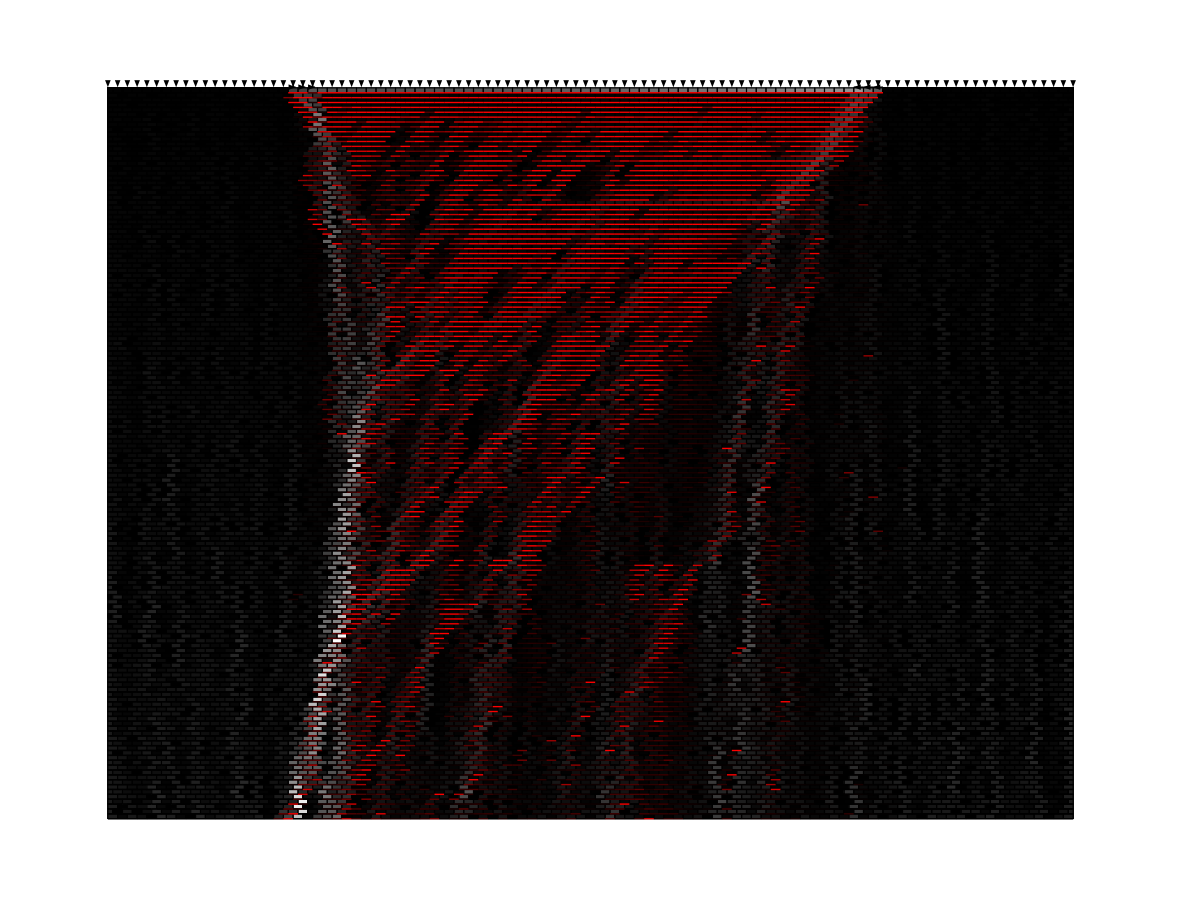

```mathematica
solveProblemAndDisplay["stress_state"]
(*displayWallWithFilter["contacts_state"]*)
```

### Compute frames

```mathematica
H1LoadingHistory[H1max_,t_]:=Piecewise[{{t,t≤H1max},{H1max,t>H1max}}];
H2LoadingHistory[H2max_,t_]:=Piecewise[{{t,t≤H2max}}];
```

```mathematica
H2max=80;H1max=40;
tmax=H2max;
frames={};
For[t=0,t≤tmax,t+=5,
p=Table[{0,0,2,0,0,0},{nelx}];
p[[20;;22]]={0,0,20,H1LoadingHistory[H1max,t],0,0};
p[[78;;80]]={0,0,20,-H2LoadingHistory[H2max,t],0,0};
p=Flatten[p];
setBoundaryConditions[p];
AppendTo[frames,solveProblemAndDisplay["stress_state"]];
];
```

## Convergent horizontal loads - plastic zones interaction

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[60,60,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[15;;17]]={0,0,40,40,0,0};
p[[43;;45]]={0,0,40,-70,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

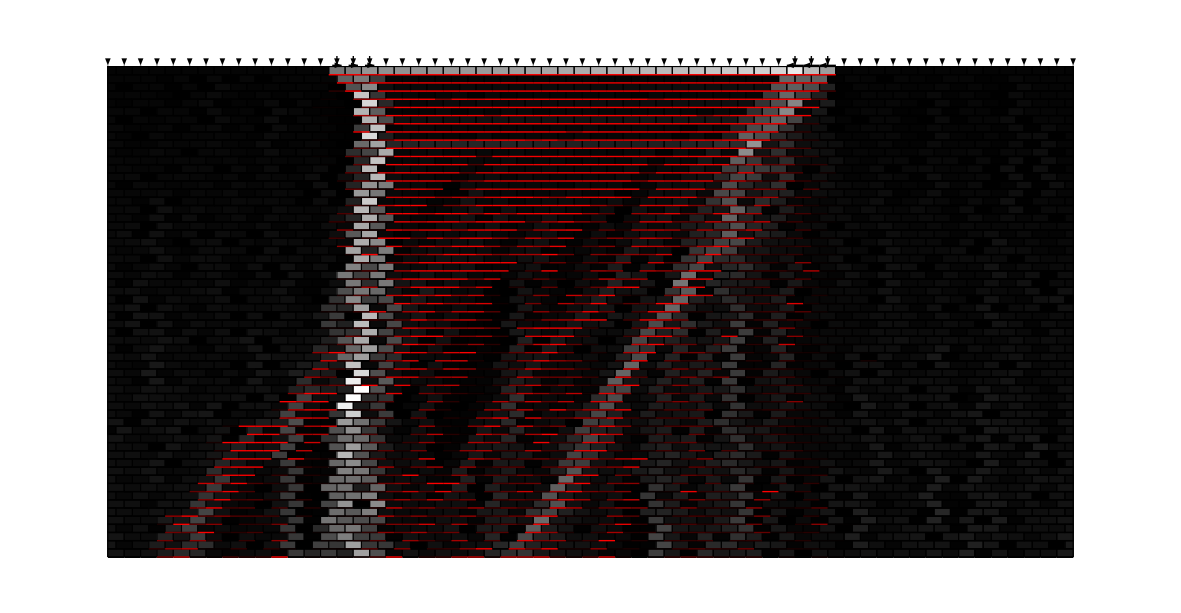

```mathematica
solveProblemAndDisplay["stress_state"]
(*displayWallWithFilter["contacts_state"]*)
```

### Compute frames

```mathematica
H1LoadingHistory[H1max_,t_]:=Piecewise[{{t,t≤H1max},{H1max,t>H1max}}];
H2LoadingHistory[H2max_,t_]:=Piecewise[{{t,t≤H2max}}];
```

```mathematica
H2max=70;H1max=40;
tmax=H2max;
frames={};
For[t=0,t≤tmax,t+=2.5,
p=Table[{0,0,2,0,0,0},{nelx}];
p[[20;;22]]={0,0,40,H1LoadingHistory[H1max,t],0,0};
p[[38;;40]]={0,0,40,-H2LoadingHistory[H2max,t],0,0};
p=Flatten[p];
setBoundaryConditions[p];
AppendTo[frames,solveProblemAndDisplay["stress_state"]];
];
```

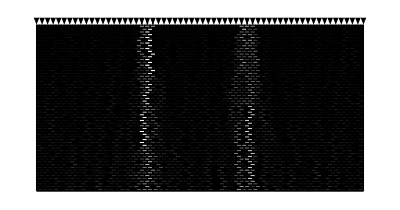
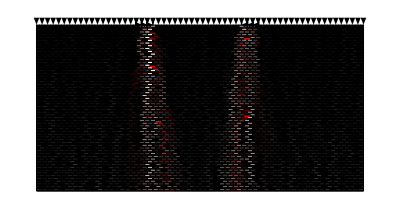
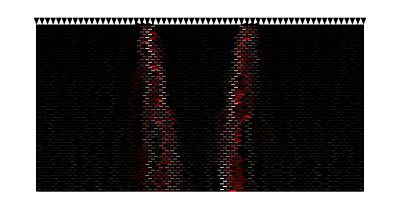
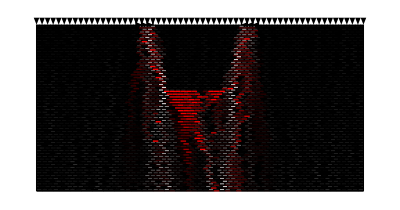
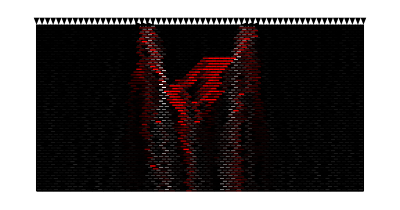
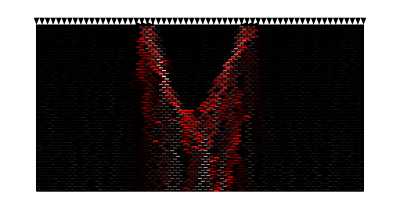
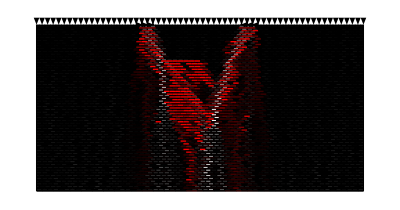
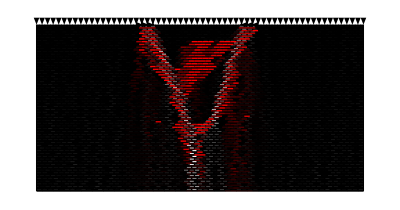
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frames
```

```mathematica
Export["test.gif",frames,ImageSize->1000,"DisplayDurations"->0.3]
```

test.gif

```mathematica
Export["test.avi",frames,ImageSize->500,"FrameRate"->2]
```

test.avi

```mathematica
frames[[15]]
```

-Graphics-

```mathematica
dwg1=-Graphics-;(*6: H=12.5*)
dwg2=-Graphics-;(*9: H=20*)
dwg3=-Graphics-;(*16: H=37.5*)
```

### Export graphics

```mathematica
Export["risultati_carichi_h_convergenti_1.pdf",dwg1,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_convergenti_1.pdf

```mathematica
Export["risultati_carichi_h_convergenti_2.pdf",dwg2,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_convergenti_2.pdf

```mathematica
Export["risultati_carichi_h_convergenti_3.pdf",dwg3,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_convergenti_3.pdf